```mathematica
V0=35;R=2;a=0.5;μ=8/9;
```

```mathematica
rmax=10.0;dr=0.1;
rlist=Range[0,rmax,dr];
```

```mathematica
n=Length[rlist]
```

101

```mathematica
V[r_]:=-V0/(1+Exp[(r-R)/a]);
```

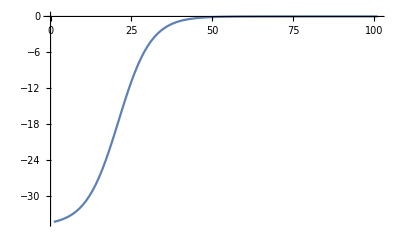

```mathematica
Vmat=DiagonalMatrix[V[rlist]];
ListLinePlot[V[rlist]]
```

```mathematica
Vmat[[n,n]]
```

-3.93873×10^-6

```mathematica
Dimensions[Vmat]
```

{101,101}

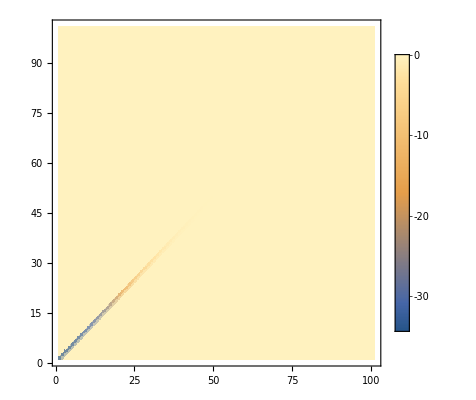

```mathematica
ListDensityPlot[Vmat,PlotLegends->Automatic]
```

```mathematica
(*calculate KE matrix*)
one[n_,d_]:=
DiagonalMatrix[1+0Range[n-Abs[d]],d];
KE=-1/(2 μ) 1/dr^2(one[n,-1]-2 one[n,0]+one[n,1]);
```

```mathematica
H0=KE+Vmat;
```

```mathematica
k[En_]:=Sqrt[-2μ En]
```

```mathematica
En=-V0/2
```

-35/2

```mathematica
Dimensions[H0]
```

{101,101}

```mathematica
Hnew=H0;Hnew[[n,n]]=Hnew[[n,n]]+KE[[n,n]]*(1-dr k[En]);
```

```mathematica
(*Hupdate[En_]:=Module[{Hnew},Hnew[[n,n]]=Hnew[[n,n]]+KE[[n,n]]*(1-dr k[En])];*)
```

```mathematica
{eval,evec}=Eigensystem[Hnew];
```

```mathematica
Manipulate[ListPlot[{rlist,evec⟦-i⟧}ᵀ,Joined->True,PlotRange->All],{i,1,n,1}]
```

```mathematica
eval
```

{224.886,224.553,224.021,223.303,222.412,221.359,220.154,218.807,217.327,215.724,214.006,212.184,210.267,208.266,206.192,204.059,201.882,199.68,197.479,195.313,193.232,191.28,189.403,187.441,185.33,183.086,180.73,178.274,175.728,173.098,170.391,167.611,164.762,161.849,158.876,155.847,152.764,149.632,146.455,143.235,139.976,136.682,133.355,130.,126.62,123.218,119.798,116.363,112.917,109.463,106.004,102.544,99.0863,95.6345,92.1918,88.7618,85.3477,81.9531,78.5812,75.2354,71.919,68.6354,65.3879,62.1796,59.0139,55.8939,52.8229,49.804,46.8403,43.9349,41.0909,38.3114,35.5993,32.9578,-30.5118,30.3898,27.8982,25.4861,-24.9328,23.1565,20.9125,-18.9776,18.7571,16.6935,14.7249,-13.0723,12.8547,11.0865,9.42406,7.87151,-7.62585,6.4334,5.11484,3.92177,-3.1263,2.86117,1.94163,1.17395,0.572615,-0.330118,0.16126}